```mathematica
Quit;
ClearAll;
Needs["VariationalMethods`"]
```

```mathematica
Action=Sqrt[1/(r^2-m/r)+r^2 x'[r]^2]
```

√(1/(-m/r+r^2)+r^2 x'[r]^2)

```mathematica
m=1;
r0=1;
rmax=80;
Sol=NDSolve[{x'[r]==√(r0^2/((r^2-m/r)(r^4-r0^2 r^2))),x[rmax]==0.1},x,{r,r0,rmax}]
x[r0]/.NDSolve[{x'[r]==√(r0^2/((r^2-m/r)(r^4-r0^2 r^2))),x[rmax]==0.1},x,{r,r0,rmax}]
```

NDSolve::ndsz: At r == 1., step size is effectively zero; singularity or stiff system suspected.

{{x→InterpolatingFunction[{{1., 80.}}, <>]}}

NDSolve::ndsz: At r == 1., step size is effectively zero; singularity or stiff system suspected.

{-10.9593}

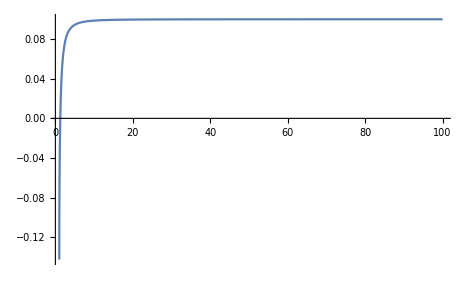

```mathematica
Plot[x[r]/.Sol,{r,r0,rmax},PlotRange->All]
```

```mathematica
A[r0_]:=2(NIntegrate[Action/.NDSolve[{x'[r]==√(r0^2/((r^2-m/r)(r^4-r0^2 r^2))),x[rmax]==0.1},x,{r,r0,rmax}],{r,r0,rmax}]-)
ℓ[r0_]:=2*Abs[x[r0]/.NDSolve[{x'[r]==√(r0^2/((r^2-m/r)(r^4-r0^2 r^2))),x[rmax]==0.1},x,{r,r0,rmax}]]
```

```mathematica
Tabes=Quiet[Partition[Flatten[Table[{A[r0],ℓ[r0]},{r0,1.0,10,0.1}],2],2]];
```

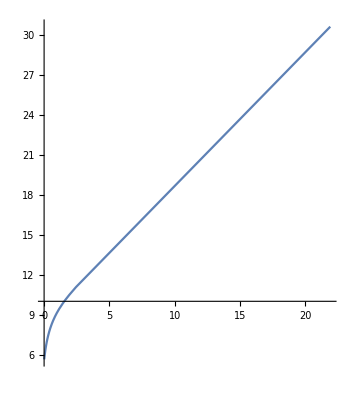

```mathematica
ListCurvePathPlot[{Tabes},PlotRange->All]
```